```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
runnumber=8;
threshold=0.0;
max=9999;
```

6

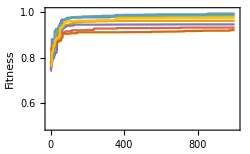

b.eps

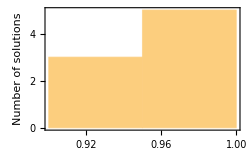

b_hist.eps

```mathematica
exp="../cSrc/15B";
maxfit=0.0;
maxind =-1;
allgens={};
allfit={};
bestgen={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens=Append[allgens,y[[2]]];
allfit=Append[allfit,Last[y[[2]]]];
If[Last[y[[2]]]>maxfit,maxfit=Last[y[[2]]];maxind=i;];
If[Last[y[[2]]]>threshold,
file = StringJoin[exp,"/",ToString[i], "/best.gen.dat"];
x = Flatten[Import[file]];
bestgen=Append[bestgen,x];
];
];

maxind
ListLinePlot[Sqrt[allgens],PlotRange->{{-10,1010},{0.49,1.01}},Frame->True,FrameLabel->{"Generations","Fitness"},ImageSize->250]
Export["b.eps",%]
Histogram[Sqrt[allfit],Frame->True,FrameLabel->{"Fitness","Number of solutions"},ImageSize->250]
Export["b_hist.eps",%]
```

```mathematica
Sort[Table[{x-1,allfit[[x]]},{x,1,100}],#1[[2]]>#2[[2]]&]
```

Part::partw: Part 9 of {0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329} does not exist.

Part::partw: Part 10 of {0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329} does not exist.

Part::partw: Part 11 of {0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{6,0.988999},{0,0.982155},{2,0.97113},{7,0.95329},{1,0.926881},{4,0.896114},{3,0.869486},{5,0.850117},{8,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦9⟧},{9,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦10⟧},{10,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦11⟧},{11,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦12⟧},{12,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦13⟧},{13,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦14⟧},{14,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦15⟧},{15,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦16⟧},{16,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦17⟧},{17,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦18⟧},{18,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦19⟧},{19,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦20⟧},{20,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦21⟧},{21,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦22⟧},{22,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦23⟧},{23,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦24⟧},{24,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦25⟧},{25,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦26⟧},{26,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦27⟧},{27,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦28⟧},{28,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦29⟧},{29,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦30⟧},{30,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦31⟧},{31,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦32⟧},{32,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦33⟧},{33,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦34⟧},{34,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦35⟧},{35,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦36⟧},{36,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦37⟧},{37,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦38⟧},{38,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦39⟧},{39,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦40⟧},{40,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦41⟧},{41,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦42⟧},{42,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦43⟧},{43,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦44⟧},{44,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦45⟧},{45,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦46⟧},{46,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦47⟧},{47,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦48⟧},{48,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦49⟧},{49,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦50⟧},{50,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦51⟧},{51,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦52⟧},{52,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦53⟧},{53,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦54⟧},{54,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦55⟧},{55,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦56⟧},{56,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦57⟧},{57,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦58⟧},{58,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦59⟧},{59,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦60⟧},{60,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦61⟧},{61,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦62⟧},{62,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦63⟧},{63,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦64⟧},{64,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦65⟧},{65,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦66⟧},{66,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦67⟧},{67,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦68⟧},{68,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦69⟧},{69,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦70⟧},{70,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦71⟧},{71,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦72⟧},{72,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦73⟧},{73,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦74⟧},{74,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦75⟧},{75,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦76⟧},{76,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦77⟧},{77,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦78⟧},{78,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦79⟧},{79,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦80⟧},{80,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦81⟧},{81,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦82⟧},{82,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦83⟧},{83,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦84⟧},{84,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦85⟧},{85,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦86⟧},{86,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦87⟧},{87,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦88⟧},{88,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦89⟧},{89,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦90⟧},{90,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦91⟧},{91,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦92⟧},{92,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦93⟧},{93,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦94⟧},{94,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦95⟧},{95,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦96⟧},{96,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦97⟧},{97,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦98⟧},{98,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦99⟧},{99,{0.982155,0.926881,0.97113,0.869486,0.896114,0.850117,0.988999,0.95329}⟦100⟧}}

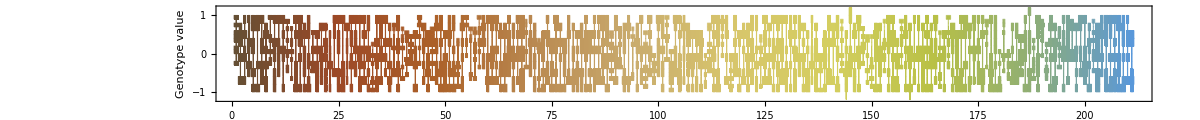

Parameters.eps

```mathematica
DistributionChart[Transpose[bestgen],ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",Frame->True,AspectRatio->1/10,FrameLabel->{"Parameters","Genotype value"},ImageSize->1200]
Export["Parameters.eps",%]
```